```mathematica
Ulj[r_] := 4 ϵ ((σ/r)^12-(σ/r)^6);
```

```mathematica
Umq[r_] := C q μ/r^2;
Uqq[r_] := C (q1 q2)/r;
```

```mathematica
(0.5)*(3.9+5.8)
```

4.85

```mathematica
(0.5)*(3.9+1.8)
```

2.85

```mathematica
(0.5)*(5.8+1.8)
```

3.8

```mathematica
2.5*4.85
```

12.125

```mathematica
SubsLJab = {ϵ->0.7014, σ->4.85};
SubsMQab  = {C-> 336, q -> -1.0, μ -> 0.354};
```

```mathematica
Uljab[r_]:= Ulj[r]/.SubsLJab;
Umqab[r_] :=   Umq[r]/.SubsMQab; 
Uab[r_] := Uljab[r] + Umqab[r];
```

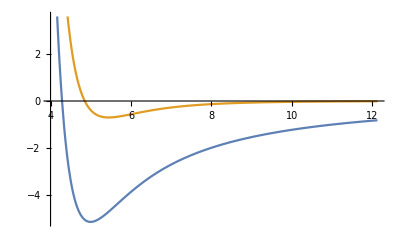

```mathematica
Plot[{Uab[r],Uljab[r]},{r,4.0,12.125}]
```

```mathematica
SubsLJcb = {ϵ->0.7014, σ->2.85};
SubsMQcb  = {C-> 336, q -> 1.0, μ ->-0.354};
```

```mathematica
Uljcb[r_]:= Ulj[r]/.SubsLJcb;
Umqcb[r_] :=   Umq[r]/.SubsMQcb; 
Ucb[r_] := Uljcb[r] + Umqcb[r];
```

```mathematica
p1 = Plot[{Ucb[r],Uab[r]},{r,2.0,12.0},PlotRange->{{2.0,12.0},{-15,5}}, PlotLegends->{"Li^+/PEO","PF_6^-/PEO"}, AxesLabel->{"r (Å)","U (kcal/mol)"},PlotStyle->{Blue, Red}];
Export["/Users/marshalltekell/Desktop/temp.pdf",p1]
```

/Users/marshalltekell/Desktop/temp.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/marshalltekell/Desktop/temp.pdf"]]]
```

```mathematica
SubsQQca = {C-> 336, q1 -> -1.0, q2-> 1.0};
SubsLJca = {ϵ->0.7014, σ->3.8};
```

```mathematica
Uqqca[r_] := Uqq[r]/.SubsQQca;
Uljca[r_] := Ulj[r]/.SubsLJca;
Uca[r_] := Uljca[r] + Uqqca[r];
```